```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
hfE = -7.862134;
gsE = -7.8807352437;
```

```mathematica
styling = {
	ImageSize->Medium,
	LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
	Frame->True,FrameStyle->Black,
	FrameTicks->{{Automatic,None},{Automatic,None}},
	GridLinesStyle -> {Red, Thick},
	GridLines->  {None, {gsE, {hfE,Dashed}}},
	PlotStyle -> {RGBColor[0,.72,1], RGBColor[.92,.59,.18]},
	PlotLegends -> Placed[
		LineLegend[
			{RGBColor[0,.72,1], RGBColor[.92,.59,.18], Directive[Red,Dashed],Red},
			{" Imaginary time", " Gradient descent", " Hartree Fock", " Ground"},
			LegendMarkerSize->20, Spacings -> .1
		], {.75,.7}]
};
```

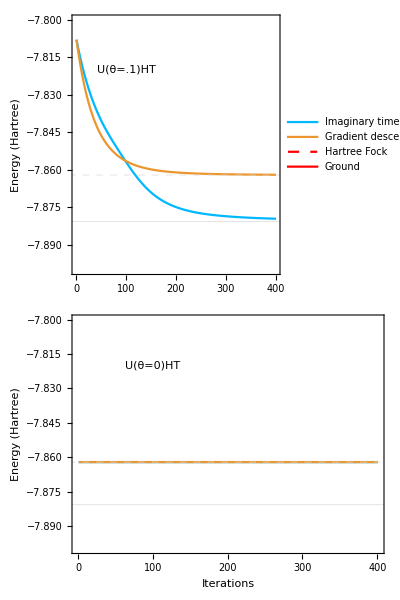

```mathematica
dataHT = Get["output_HT.txt"];
htplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	PlotLegends->None,
	Sequence @@ styling,

	Epilog -> Style[Text["U(θ=0)HT",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
];

dataNearHT = Get["output_nearHT.txt"];
nearhtplot = ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{None,"Energy (Hartree)"},
	Sequence @@ styling,
	
	Epilog -> Style[Text["U(θ=.1)HT",{100,-7.82}], 12,FontFamily->"Latin Modern Roman"]
];

Column[{
 nearhtplot,htplot
}, Spacings->-2.4]
```

```mathematica
Export["nearHT.pdf",%]
```

nearHT.pdf

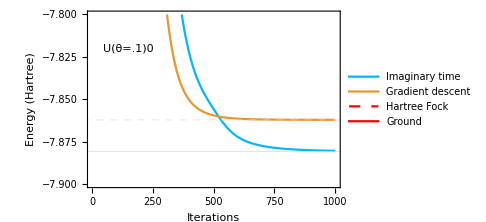

```mathematica
dataNearZero = Get["output_nearZeroState.txt"];
ListLinePlot[
	{%["imagEnergies"],%["gradEnergies"]},
	PlotRange->{-7.9, -7.8},
	FrameLabel->{"Iterations","Energy (Hartree)"},
	Sequence @@ styling,
	
Epilog -> Style[Text["U(θ=.1)0",{150,-7.82}], 12,FontFamily->"Latin Modern Roman"]
]
```

```mathematica
Export["nearZero.pdf", %]
```

nearZero.pdf